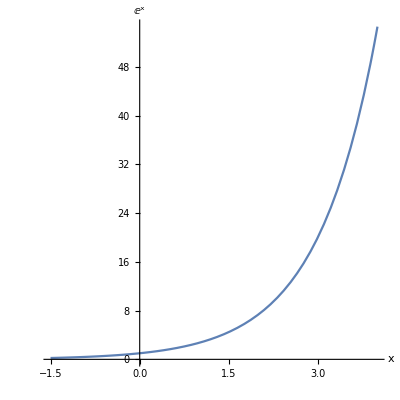

```mathematica
exp=Plot[Exp[x],{x,-1.5, 4}, AspectRatio->1, AxesLabel->{x,Exp[x]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}]
```

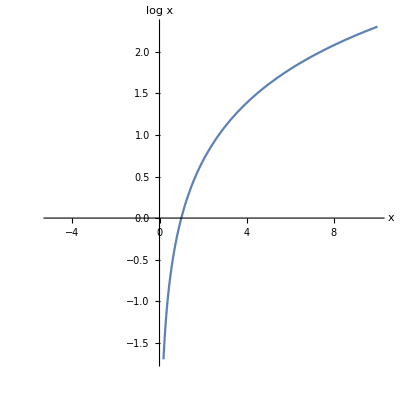

```mathematica
log=Plot[Log[x],{x, -5, 10}, AspectRatio->1,
 AxesLabel->{x,
Style["log",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}]
```

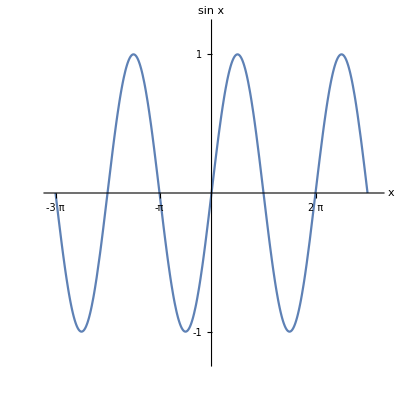

```mathematica
sin=Plot[Sin[x], {x, -3Pi, 3Pi}, AspectRatio->1, 
AxesLabel->{x,
Style["sin",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},
LabelStyle->{FontFamily->"STIX Two Text"},
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
Ticks->{{-3Pi,-2Pi,-Pi,Pi,2Pi,3Pi},{-1, 1}},
PlotRange->{{-3Pi-0.3, 3Pi+0.6},{-1.2, 1.2}}]
```

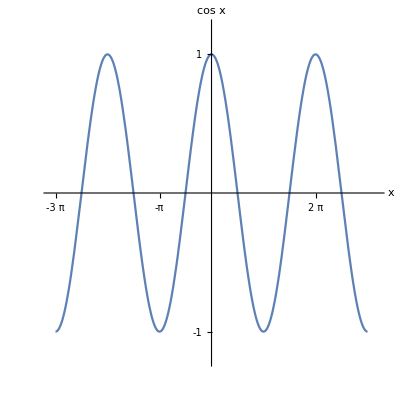

```mathematica
cos=Plot[Cos[x],{x,-3Pi, 3Pi}, AspectRatio->1, 
AxesLabel->{x,
Style["cos",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
Ticks->{{-3Pi,-2Pi,-Pi,Pi,2Pi,3Pi},{-1, 1}},
PlotRange->{{-3Pi-0.3, 3Pi+0.6},{-1.2, 1.2}}]
```

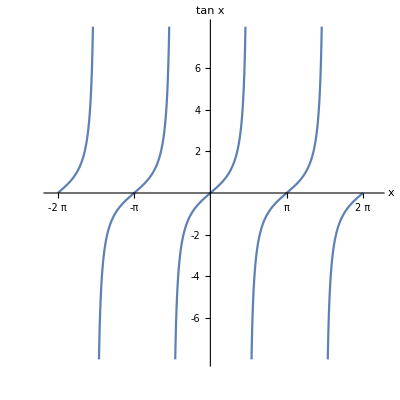

```mathematica
tan=Plot[Tan[x], {x, -2Pi, 2Pi}, 
 AspectRatio->1, 
AxesLabel->{x,
Style["tan",FontFamily-> "STIX Two Text"]Style["x",FontFamily-> "STIX Two Text", Italic]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
Ticks->{{-2Pi,-Pi,Pi,2Pi},{-6, -4,-2,2,4,6}},
PlotRange->{{-2Pi-0.3, 2Pi+0.6},{-8, 8}}]
```

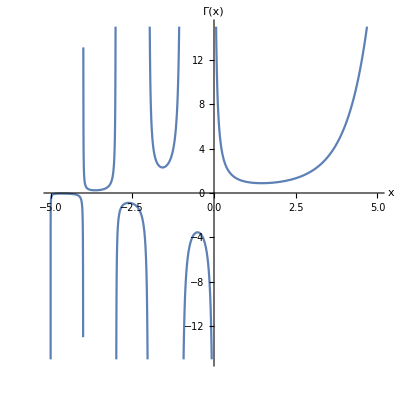

```mathematica
gamma=Plot[Gamma[x], {x, -5, 5}, 
PlotRange->{{-5, 5},{-15, 15}},
AspectRatio->1, 
AxesLabel->{x,Γ[x]},
LabelStyle->(FontFamily->"STIX Two Text"),
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}]
```

```mathematica
Export["D:\\wolfram\\cos.pdf",cos]
Export["D:\\wolfram\\sin.pdf",sin]
Export["D:\\wolfram\\tan.pdf",tan]
Export["D:\\wolfram\\log.pdf",log]
Export["D:\\wolfram\\exp.pdf",exp]
Export["D:\\wolfram\\gamma.pdf",gamma]
```

D:\wolfram\cos.pdf

D:\wolfram\sin.pdf

D:\wolfram\tan.pdf

D:\wolfram\log.pdf

D:\wolfram\exp.pdf

D:\wolfram\gamma.pdf